```mathematica
SetDirectory["~/Desktop/UPenn/Financial Engineering/Assignment 1"];
```

```mathematica
OptData=Import["GOOGOptions.csv"];
```

```mathematica
TableForm[OptData[[Range[7]]]]
```

secid | ticker | exercise_style | date | close | rate | exdate | last_date | cp_flag | strike_price | best_bid | best_offer | volume | open_interest
121812 | GOOG | A | 6/22/07 | 524.98 | 0 | 7/21/07 | 6/22/07 | C | 290000 | 235.6 | 236.5 | 20 | 130
121812 | GOOG | A | 6/22/07 | 524.98 | 0 | 7/21/07 |  | P | 290000 | 0 | 0.05 | 0 | 0
121812 | GOOG | A | 6/22/07 | 524.98 | 0 | 7/21/07 | 6/22/07 | C | 300000 | 225.7 | 226.6 | 1 | 116
121812 | GOOG | A | 6/22/07 | 524.98 | 0 | 7/21/07 |  | P | 300000 | 0 | 0.05 | 0 | 0
121812 | GOOG | A | 6/22/07 | 524.98 | 0 | 7/21/07 | 6/21/07 | C | 310000 | 215.7 | 216.6 | 0 | 100
121812 | GOOG | A | 6/22/07 | 524.98 | 0 | 7/21/07 | 6/20/07 | P | 310000 | 0 | 0.05 | 0 | 101

```mathematica
QuoteDate=Drop[OptData[[All,4]],1];
Svec=Drop[OptData[[All,5]],1];
δvec=Drop[OptData[[All,6]],1]/100;
ExDate=Drop[OptData[[All,7]],1];
CPvec=Drop[OptData[[All,9]],1];
Kvec=Drop[OptData[[All,10]],1]/1000;
Bidvec=Drop[OptData[[All,11]],1];
Askvec=Drop[OptData[[All,12]],1];

Tvec=(MapThread[DateDifference,{QuoteDate,ExDate}]-1)/365;
Midvec=(Bidvec+Askvec)/2;
```

```mathematica
IntData=Import["ZeroCurve.csv"]; (*LIBOR zero coupon yield curve*)
```

```mathematica
TableForm[IntData[[Range[7]]]]
```

date | days | rate
06/22/2007 | 7 | 5.41125
06/22/2007 | 14 | 5.39232
06/22/2007 | 26 | 5.38454
06/22/2007 | 54 | 5.40194
06/22/2007 | 89 | 5.40124
06/22/2007 | 117 | 5.39923

```mathematica
IntMaturities=Drop[IntData[[All,2]],1]/365;
IntRates=Drop[IntData[[All,3]],1]/100;
```

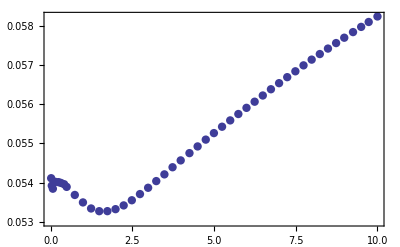

```mathematica
ListPlot[Transpose[{IntMaturities,IntRates}],Frame->True,Axes->False,PlotStyle->PointSize[0.015]]
```

```mathematica
PrependTo[IntMaturities,0];
PrependTo[IntRates,IntRates[[1]]];
```

```mathematica
ZeroCurve=Interpolation[Transpose[{IntMaturities,IntRates}],InterpolationOrder->1]; (*compute the interest rate corresponding to each option expiration by linear interpolation*)
```

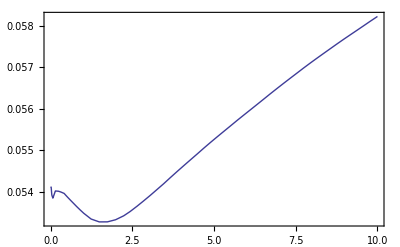

```mathematica
Plot[ZeroCurve[t],{t,0,10},Frame->True,Axes->False]
```

```mathematica
(*computes the forward prices for each option expiration using the dividend rates using cost-of-carry*)
rvec=ZeroCurve[Tvec];
Gvec1=Svec Exp[(rvec- δvec)Tvec];
```

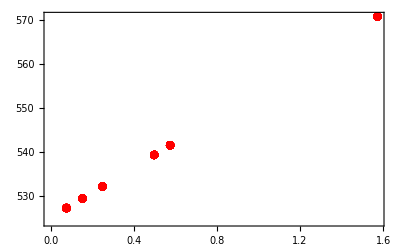

```mathematica
Gplot1=ListPlot[Transpose[{Tvec,Gvec1}],Frame->True,Axes->False,PlotStyle->{PointSize[0.015],Red}]
```

```mathematica
(*compute forward prices using the put-call parity*)
pos=Flatten[Position[CPvec,"C"]];
Gvec2=Kvec[[pos]]+(Midvec[[pos]]-Midvec[[pos+1]]) Exp[rvec[[pos]]Tvec[[pos]]];
```

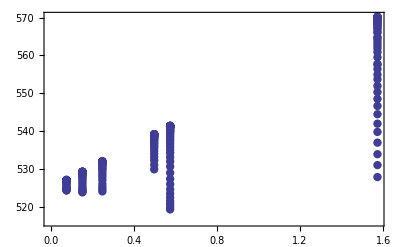

```mathematica
Gplot2=ListPlot[Transpose[{Tvec[[pos]],Gvec2}],Frame->True,Axes->False,PlotStyle->PointSize[0.015]]
```

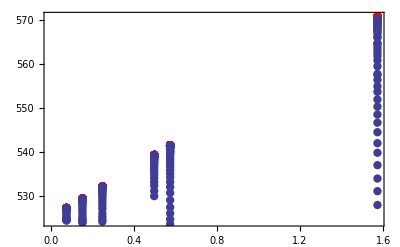

```mathematica
Show[Gplot1,Gplot2]
```

```mathematica
(*(*Construct a list that contains the different expirations T*)
Tvalues=Union[Tvec];
(*For the shortest expiration, use cost-of-carry formula*)
Gvalues={Gvec1[[1]]};
(*For other expirations, compute the fwd price from put-call parity*)
Do[
(*For each expiration T, identify the options expiring at T*)
T=Tvalues[[i]];
pos=Select[Flatten[Position[Tvec,T]],OddQ];
(*Identify the ATM strike*)
CPSpreads=Midvec[[pos]]-Midvec[[pos+1]];
Strikes=Kvec[[pos]];
pos=First[Flatten[Position[Abs[CPSpreads],Min[Abs[CPSpreads]]]]];
(*Compute the forward price for expiration T*)
AppendTo[Gvalues,Strikes[[pos]]+CPSpreads[[pos]]Exp[ZeroCurve[T]T]],
(*Repeat for each expiration T other than the shortest one*)
{i,2,Length[Tvalues]}
];*)
(*Construct a list that contains the different expirations T*)
Tvalues=Union[Tvec];
(*For the shortest expiration, use cost-of-carry formula*)
Gvalues=Union[Gvec1];
```

```mathematica
Tvalue=Flatten[Map[Position[Tvalues,#]&,Tvec]];
Gvec=Union[Gvec1][[Tvalue]];
```

```mathematica
BSCallIV[S_,K_,δ_,r_,T_,value_]:=
If[value==0,"Indeterminate",
Check[
FinancialDerivative[{"European","Call"}, {"StrikePrice"->K, "Expiration"->T,"Value"->value},  {"InterestRate"-> r, "CurrentPrice"->S, "Dividend"->δ},"ImpliedVolatility"],
"Indeterminate"]
];
```

```mathematica
BSPutIV[S_,K_,δ_,r_,T_,value_]:=
If[value==0,"Indeterminate",
Check[
FinancialDerivative[{"American","Put"}, {"StrikePrice"->K, "Expiration"->T,"Value"->value},  {"InterestRate"-> r, "CurrentPrice"->S, "Dividend"->δ},"ImpliedVolatility"],
"Indeterminate"]
];
```

```mathematica
BCallIV[G_,K_,r_,T_,value_]:=BSCallIV[G,K,r,r,T,value];

BPutIV[G_,K_,r_,T_,value_]:=BSPutIV[G,K,r,r,T,value];

BIV[G_,K_,r_,T_,CP_,value_]:=If[CP=="C",BCallIV[G,K,r,T,value],BPutIV[G,K,r,T,value]]
```

```mathematica
pos={};
Do[
If[
CPvec[[i]]=="C"&&Gvec[[i]]<Kvec[[i]],
AppendTo[pos,i]],
{i,Length[CPvec]}
];
Gvec=Gvec[[pos]];
Kvec=Kvec[[pos]];
rvec=rvec[[pos]];
Tvec=Tvec[[pos]];
CPvec=CPvec[[pos]];
Bidvec=Bidvec[[pos]];
Askvec=Askvec[[pos]];
Midvec=Midvec[[pos]];
```

```mathematica
BidIVvec=Table[
Quiet[BIV[Gvec[[i]],Kvec[[i]],rvec[[i]],Tvec[[i]],CPvec[[i]],Bidvec[[i]]]],
{i,Length[Bidvec]}
];

AskIVvec=Table[
Quiet[BIV[Gvec[[i]],Kvec[[i]],rvec[[i]],Tvec[[i]],CPvec[[i]],Askvec[[i]]]],
{i,Length[Askvec]}
];

MidIVvec=Table[
Quiet[BIV[Gvec[[i]],Kvec[[i]],rvec[[i]],Tvec[[i]],CPvec[[i]],Midvec[[i]]]],
{i,Length[Midvec]}
];
```

```mathematica
pos1=Flatten[Position[BidIVvec,x_/;NumberQ[x]]];
pos2=Flatten[Position[AskIVvec,x_/;NumberQ[x]]];
pos=Intersection[pos1,pos2];

Gvec=Gvec[[pos]];
Kvec=Kvec[[pos]];
rvec=rvec[[pos]];
Tvec=Tvec[[pos]];
CPvec=CPvec[[pos]];
BidIVvec=BidIVvec[[pos]];
AskIVvec=AskIVvec[[pos]];
MidIVvec=MidIVvec[[pos]];
```

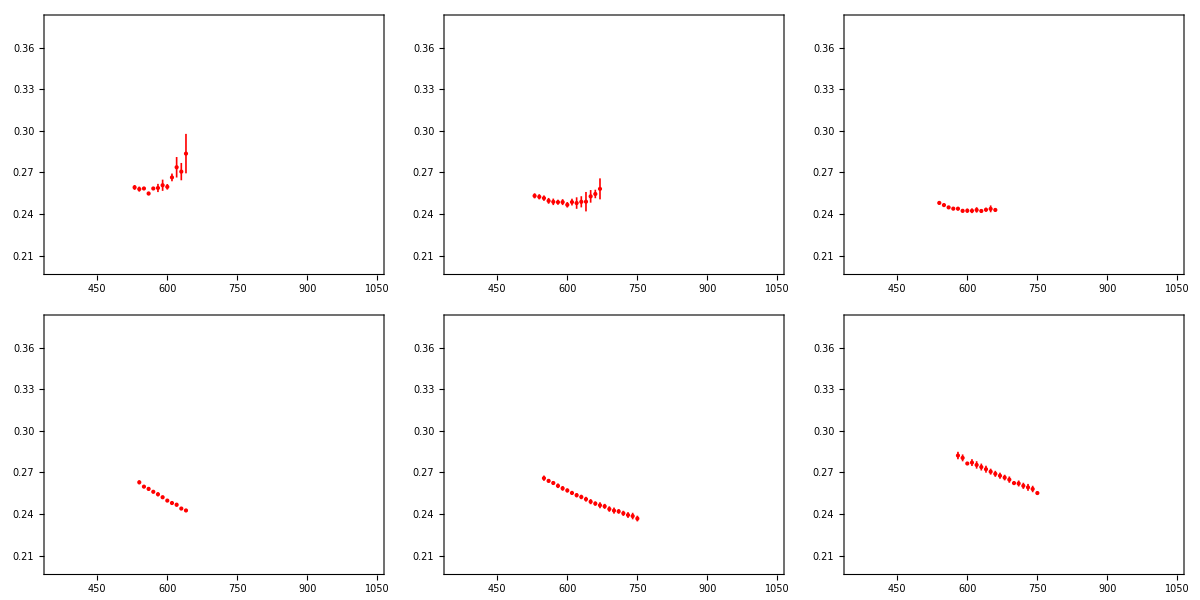

```mathematica
Needs["ErrorBarPlots`"];
Do[
pos=Flatten[Position[Tvec,Tvalues[[i]]]];
IVplot[i]=ErrorListPlot[
Table[{{Kvec[[j]],MidIVvec[[j]]},ErrorBar[MidIVvec[[j]]-BidIVvec[[j]],AskIVvec[[j]]-MidIVvec[[j]]]},
{j,Min[pos],Max[pos]}
],
Frame->True,Axes->False,PlotRange->{{350,1050},{.2,.38}},PlotStyle->{Thickness[.003],Red},
ImageSize->Scaled[.3],ImagePadding->20
],
{i,Length[Tvalues]}
];
Grid[
{{IVplot[1],IVplot[2],IVplot[3]},
{IVplot[4],IVplot[5],IVplot[6]}}
]
```

```mathematica
SVI[k_,a_,b_,σ_,ρ_,m_]:=a+b (ρ (k-m)+√((k-m)^2+σ^2));
IVSSE[a_,b_,σ_,ρ_,m_]:=Apply[Plus,(MidIVvec-Sqrt[SVI[Log[Kvec/Gvec],a,b,σ,ρ,m]])^2];

Clear[k];Clear[a];Clear[b];Clear[σ];Clear[ρ];Clear[m];
sol=NMinimize[{sse=IVSSE[a,b,σ,ρ,m],
a^2-b^2*σ^2*(1-ρ^2)≤0&&b≥0&&σ≥0&&Abs[ρ]-1≤0&&b*(1+Abs[ρ])-2/Tvalues[[2]]≤0},
{a,b,σ,ρ,m},Method->"NelderMead"]
```

NMinimize::nrnum: The function value -16.6247 - 28.3495\ ⅈ is not a real number at {a, b, m, ρ, σ} = {-0.488654, 0.27111, 0.417592, 1.4613, 0.755275}.

{6.38516,{a→0.271454,b→0.0000800015,m→0.733419,ρ→0.395449,σ→1.84494}}

```mathematica
PaddedForm[
Grid[
Prepend[Transpose[{avec,bvec,mvec,σvec,ρvec,RMSEvec}],{"a","b","m","σ_0","ρ","RMSE"}],
Dividers->{{},{1->True,2->True,10->True}}
],
{7,4}]
```

a  | b | m | σ_0 | ρ | RMSE
-111.0376 |  298.4598 |    0.6674 |    0.5714 |    0.7589 |    0.0090
  -0.3370 |   10.4410 |    0.3222 |    0.0987 |    0.9421 |    0.0011
  -0.2190 |    5.8850 |    0.3850 |   -0.1119 |    0.9382 |    0.0009
  -0.8124 |    4.2092 |    0.9089 |   -0.4205 |    0.8851 |    0.0022
  -0.2196 |    2.0906 |    0.7798 |    0.2609 |    0.9081 |    0.0013
  -0.5290 |    1.3755 |   -2.1704 |   -1.1003 |   -0.9369 |    0.0026
   0.0112 |    0.0388 |    0.1218 |    0.0707 |   -1.0000 |    0.0005
   0.0104 |    0.0360 |    0.1376 |    0.1383 |   -1.0000 |    0.0001

```mathematica
avec
bvec
mvec
σvec
ρvec
RMSEvec
```

{-111.03757499973762895091015672128,-0.33695638250262855434394709500854,-0.21898025505487724492354140802304,-0.81243423364037406555575546266203,-0.21961818011237092308264569128272,-0.5290265290659319811666636830791,0.011209265871754472086094764084135,0.01044216233014696977724341793057}

{298.45980700615315027692665676313,10.440956477934464156299636103252,5.8850226340256906282863790101073,4.2091675479694711486885124819177,2.0905697260722521480788894031774,1.3754989360057863101060597088348,0.038774367552558787502371194287116,0.035950307478226506742493977800152}

{0.66740412093805210295308313258038,0.32219309910218156228020998624059,0.38497860044949406326042385209449,0.90892934934874272871565620083426,0.77976963538571053536153085578074,-2.1703881410670603258806107763488,0.12183164338637253296952914224851,0.13758570056766863831821277193195}

{0.57140178215323693381387626617941,0.098714225650925919329889047095859,-0.11185352416431447473407896109769,-0.42050727913146740989003459051708,0.26087234374586836414635563859801,-1.100324493073603585393370032908,0.070679853093238710421953434281431,0.13832455621882819007675237010967}

{0.75893688587223124702548370311623,0.94213794690477763326648714150214,0.93818286000328864851589460482903,0.88511921140403192104376526132619,0.90812628179879224572578932528468,-0.936921583071377064601011778635,-1.000000000000000033683797415568,-1.0000000000000000279357153532244}

{0.00904970972549787568554728497,0.001051595324183401653113065626,0.0009144474595345654119206689179,0.002186856979810991650121353009,0.001266884026976800555743293985,0.002611987574145735126257234043,0.00048786071842867075263569074769,0.00013913572468303880034665551994}

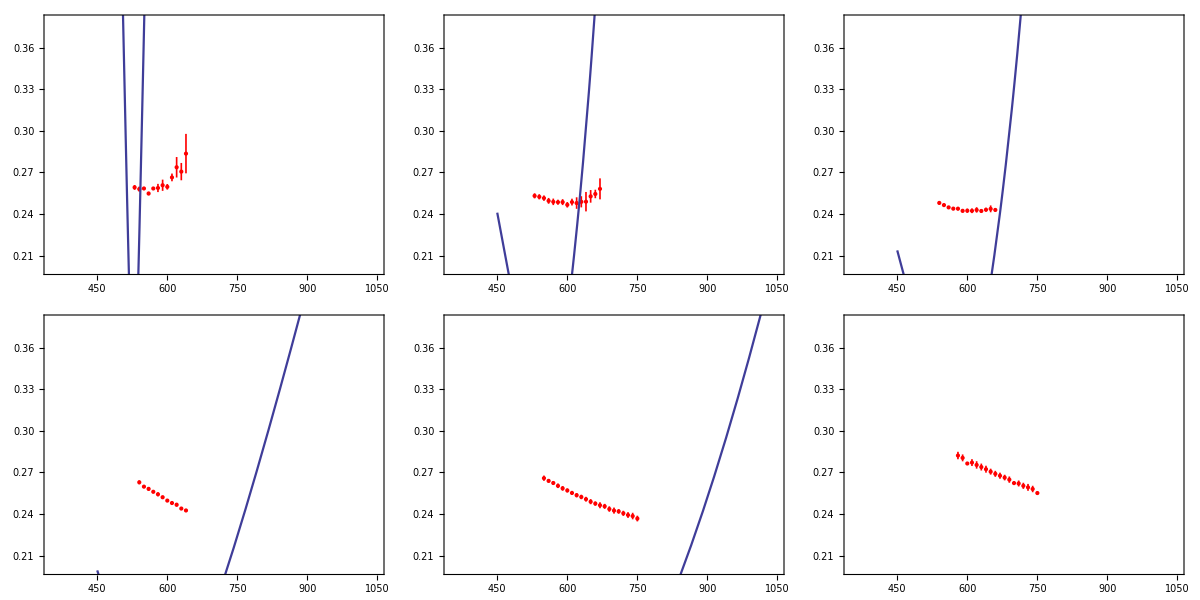

```mathematica
Do[
G=Gvec[[First[pos[i]]]];
plot=Plot[
Sqrt[SVI[Log[K/G],avec[[i]],bvec[[i]],σvec[[i]],ρvec[[i]],mvec[[i]]]],
{K,450,1650},
Axes->False,Frame->True,PlotStyle->Thickness[.004]];
SVIplot[i]=Show[{IVplot[i],plot}],
{i,Length[Tvalues]}
];
Grid[
{{SVIplot[1],SVIplot[2],SVIplot[3]},
{SVIplot[4],SVIplot[5],SVIplot[6]}}
]
```

```mathematica
VS[K_,T_]:=
Interpolation[Transpose[{Tvalues,Sqrt[SVI[Log[K/Gvalues],avec,bvec,σvec,ρvec,mvec]]}],InterpolationOrder->1][T]
```

```mathematica
Plot3D[VS[K,T],{K,350,600},{T,Tvalues[[1]],Tvalues[[-1]]},AxesLabel->{"K","T-t",""},Boxed->False,PlotRange->Automatic]
```

Thread::tdlen: Objects of unequal length in {-0.409507, -0.413664, -0.418842, -0.432246, -0.436343, -0.489153} + {-0.66740412093805210295308313258038, -0.32219309910218156228020998624059, -0.38497860044949406326042385209449, -0.90892934934874272871565620083426, -0.77976963538571053536153085578074, 2.1703881410670603258806107763488, -0.12183164338637253296952914224851, -0.13758570056766863831821277193195} cannot be combined.

General::stop: Further output of Thread :: tdlen will be suppressed during this calculation.

Transpose::nmtx: The first two levels of the one-dimensional list {{28/365, 56/365, 91/365, 182/365, 42/73, 574/365}, « 1 »} cannot be transposed.

Interpolation::innd: First argument in Transpose[{{28/365, 56/365, 91/365, 182/365, 42/73, 574/365}, « 1 »}] does not contain a list of data and coordinates.

Transpose::nmtx: The first two levels of the one-dimensional list {{0.0767123, 0.153425, 0.249315, 0.49863, 0.575342, 1.5726}, {√-111.038 + 298.46\ (0.758937\ Plus[« 2 »] + √Plus[« 2 »]), √-0.336956 + 10.441\ (0.942138\ Plus[« 2 »] + √Plus[« 2 »]), √-0.21898 + 5.88502\ (0.938183\ Plus[« 2 »] + √Plus[« 2 »]), √-0.812434 + 4.20917\ (0.885119\ « 1 » + √« 1 »), √« 1 », √-0.529027 + 1.3755\ (-0.936922\ Plus[« 2 »] + √Plus[« 2 »]), √0.0112093  + 0.0387744\ (-1.\ Plus[« 2 »] + √Plus[« 2 »]), √0.0104422  + 0.0359503\ (-1.\ Plus[« 2 »] + √Plus[« 2 »])}}
 cannot be transposed.

Interpolation::innd: First argument in Transpose[{{0.0767123, 0.153425, 0.249315, 0.49863, 0.575342, 1.5726}, {√-111.038 + 298.46\ (Times[« 2 »] + Power[« 2 »]), √-0.336956 + 10.441\ (Times[« 2 »] + Power[« 2 »]), √-0.21898 + 5.88502\ (Times[« 2 »] + Power[« 2 »]), √-0.812434 + 4.20917\ (Times[« 2 »] + Power[« 2 »]), √-0.219618 + 2.09057\ (Times[« 2 »] + Power[« 2 »]), √-0.529027 + 1.3755\ (Times[« 2 »] + Power[« 2 »]), √0.0112093  + 0.0387744\ (Times[« 2 »] + Power[« 2 »]), √0.0104422  + 0.0359503\ (Times[« 2 »] + Power[« 2 »])}}]
 does not contain a list of data and coordinates.

Transpose::nmtx: The first two levels of the one-dimensional list {{28/365, 56/365, 91/365, 182/365, 42/73, 574/365}, « 1 »} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

Interpolation::innd: First argument in Transpose[{{28/365, 56/365, 91/365, 182/365, 42/73, 574/365}, « 1 »}] does not contain a list of data and coordinates.

General::stop: Further output of Interpolation :: innd will be suppressed during this calculation.

-Graphics3D-